```mathematica
ClearAll;
```

```mathematica
kEC = 1.60217733 10^-19;
kAMC = 1.660538921 10^-27;
kC=(2 kEC)/kAMC;
```

```mathematica
A[m_,V_,L_]:=(V kEC)/(m kAMC L) (*Accelation at MCP-GND -- MCP-IN *)
```

```mathematica
A2V[m_,A_,L_]:=(A kAMC L m)/kEC  (* 2nd Accelerator voltage from time *)
```

```mathematica
caTOF[a_,L_,v_]:=(-v+√(2 a L+v^2))/a (* Constant Accelerated TOF *)
```

```mathematica
t2A[t_,L_,v_]:=(-2 (-L+t v))/t^2            (* Acceleration from time, length and initial velocity *)
```

```mathematica
acceleratorVoltage[t_,length_,m_]:=(length^2 m)/(t^2 kC);    (* Ion push accelerator voltage *)
```

```mathematica
d = { 0.06626, 0.30512, 0.66273,  0.0 };                         (* Instrument dimension *)
L[n_] := d[[3]]  n                                                                           (* Compute length (m) at n-laps *)
fLength[n_]:=d[[1]] + d[[1]] + d[[2]] + d[[4]] + n  d[[3]]  (*length with compensation *)
sLength[n_] := d[[1]] + d[[1]] + d[[2]] + n  d[[3]]   (* flight length w/o compensation *)
```

```mathematica
T[m_,V_,L_]:=(L √m)/(√V √kC)
```

```mathematica
t2m[t_,V_,L_]:=(kC t^2 V)/L^2
```

```mathematica
mAr = 39.96183454;
mMe = 16.03075155;
mN2 = 28.00559943;
mXe = 131.9036049;
```

```mathematica
Me = {{6.3371784 10^-05,20},{9.9921119 10^-05,32},{1.5474489 10^-04,50}};
N2 ={{8.3684315 10^-05,20},{1.2393971 10^-04,30}};
Ar = { {9.9916768 10^-5, 20},{1.4800454 10^-4,  30 }};
Xe = { {1.8133327 10^-04, 20},{2.6869789 10^-04, 30},{4.4342763 10^-04, 50}  };
M = { Me,N2,Ar,Xe};
masses = {mMe, mN2,mAr,mXe};
```

```mathematica
(*mm[[mass]][[ [tof,lap],[tof,lap] ]]*)
MM = {{ mMe,{{6.3371784 10^-05,20},{9.9921119 10^-05,32}}}
,{mMe, {{9.9921119 10^-05,32},{1.5474489 10^-04,50}}}
,{mN2,{{8.3684315 10^-05,20},{1.2393971 10^-04,30}}}
,{mAr,{{9.9916768 10^-5, 20},{1.4800454 10^-4,  30 }}}
,{mXe,{{1.8133327 10^-04, 20},{2.6869789 10^-04, 30}}}
,{mXe,{{2.6869789 10^-04, 30},{4.4342763 10^-04, 50}}}
};
MTOF = {{ mMe,{6.3371784 10^-05,20}}
,{mMe, {9.9921119 10^-5,32}}
,{mMe,{1.5474489 10^-4,50}}
,{mN2,{8.3684315 10^-5,20}}
,{mN2,{1.2393971 10^-4,30}}
,{mAr,{9.9916768 10^-5, 20}}
,{mAr,{1.4800454 10^-4,  30 }}
,{mXe,{1.8133327 10^-4, 20}}
,{mXe,{2.6869789 10^-4, 30}}
,{mXe,{4.4342763 10^-4, 50}}
};
```

```mathematica
fVelocity[dlap_] := d[[3]]/(dlap[[1]]/dlap[[2]])
tlap[mat_] := mat[[1]]/mat[[2]];                                       (*lap-time*)
tHalfCycle[a_,b_] := b[[1]]-tlap[b-a]*b[[2]]  (* flight-time for half-cycle part *)
lHalfCycle[mm_]         := tHalfCycle[mm[[2,2]],mm[[2,1]]] * fVelocity[mm[[2,2]]-mm[[2,1]]];
halfCycleTime[mm_] := mm[[2,2]][[1]]-tlap[mm[[2,2]]-mm[[2,1]]]*mm[[2,2]][[2]];
```

#### Accelerator voltage estimation

```mathematica
(*hfunctor[mm_] := tHalfCycle @@ mm;; hfunctor /@ MM[[All,2]] *)
MM[[All,1]];
hcTimes = tHalfCycle @@ #& /@ MM[[All,2]]; (* time for half-cycle mode *)
hcLength = lHalfCycle /@ MM;
hcVa = acceleratorVoltage @@ #& /@ Transpose[{hcTimes,hcLength,MM[[All,1]]}];
```

### TOF Equation (scan law) on orbital period

```mathematica
dMM = MM[[All,2,2]]-MM[[All,2,1]];
```

FittedModel[6.32768×10^-10+1.14781×10^-6 x]

{6.32768×10^-10,1.14781×10^-6}

3933.4

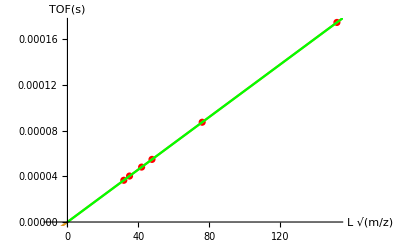

```mathematica
tlaps = Transpose[{ Sqrt[MM[[All,1]]] * L[dMM[[All,2]]],dMM[[All,1]] }]; (* (Sqrt[m]*L), tof *)
m0 = LinearModelFit[tlaps, x, x]
{offset0,slope0}=CoefficientList[ Normal[m0],x]
oT[m_,L_] := (offset0 + slope0 *Sqrt[m ])* L
oM[t_, L_] := ((-offset0 * L + t)/(slope0*L))^2
Va = acceleratorVoltage[slope0 ,1,1] (* mass = 1, length = 1m *)
Show[ListPlot[tlaps, PlotStyle -> Red,PlotRange->{{-10,All},Full}]
      ,Plot[{line, m0[x]},{x,-100,400}]
   ,Plot[oT[x^2,1],{x,0,400},PlotStyle->Green]
      ,AxesLabel->{L Sqrt[m/z],"TOF(s)"}]
```

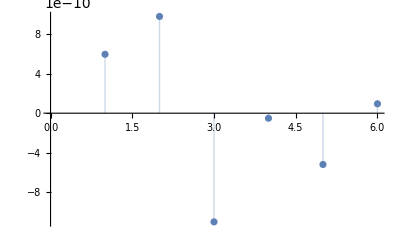

```mathematica
ListPlot[m0["FitResiduals"], Filling -> Axis]
```

### Compensation length calculation

{2.28581×10^-7,5.16335×10^-8}

0.0449595

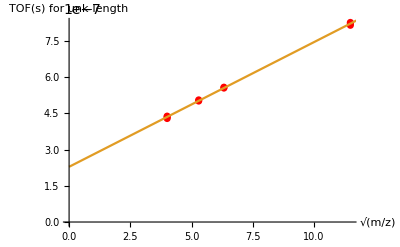

0.044959528

```mathematica
{mass,tof,lap} = {MTOF[[All,1]],MTOF[[All,2,1]],MTOF[[All,2,2]]};
uTOF = Transpose[ {Sqrt[mass],(tof  - oT[ mass,sLength[lap] ])}];
pu = LinearModelFit[uTOF, x,x];
uEq = CoefficientList[Normal[pu], x]
d[[4]] =uEq[[2]]/oT[1,1]
Show[ListPlot[uTOF, PlotStyle -> Red, PlotRange -> {{0,All}, {0,All}}]
       , Plot[{line, pu[x]}, {x, 0, 12}], AxesLabel -> {Sqrt[m/z], "TOF(s) for unk-length"}]
NumberForm[d[[4]],8]
```

```mathematica
ListPlot[pu["FitResiduals"], Filling -> Axis];
```

## 4mm scan law

```mathematica
{mass,tof,lap}={MTOF[[All,1]],MTOF[[All,2,1]],MTOF[[All,2,2]]};
```

FittedModel[2.19774×10^-7-0.0000159243 x]

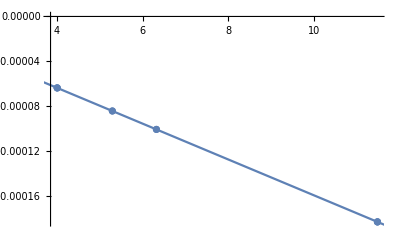

{2.19774×10^-7,-0.0000159243}

```mathematica
dTOF = tof - oT[mass,fLength[lap]-Ld]/.Ld->0.004;
dModel = LinearModelFit[ Transpose[{Sqrt[mass],dTOF}],x,x]
Show[ ListPlot[ Transpose[{Sqrt[mass],dTOF}]], Plot[ dModel[x], {x,1,12}] ]
{a,b} = CoefficientList[Normal[dModel],x]
```

```mathematica
A2V[m,t2A[ b, Ld,1/T[m,Va,1]],Ld]/.{m->1,Ld->0.004}
```

4.53758

### #################################

```mathematica
A2V[m,t2A[ caTOF[A[m,5000,Ld], Ld, 1/T[m,Va,1]], Ld, 1/T[m,Va,1]],Ld]/.{Ld->0.004,m->{1,16,28,40,44,132}}
```

{5000.,5000.,5000.,5000.,5000.,5000.}

```mathematica
(* dt = a + b Sqrt[m] *)
(* dt for m/z 1 = a + b *)
A2V[m,t2A[ b, Ld,1/T[m,Va,1]],Ld]/.{m->1,Ld->0.003}
```

3.40294

```mathematica
A2V[1,t2A[ dvelocity, Ld,1/T[1,Va,1]],Ld]/.{Ld->0.004}
```

-(8.29141×10^-11 (-0.004+871224. dvelocity))/dvelocity^2